```mathematica
<<KerrQNMs`
```

```mathematica
ω1=KerrQNM[2,2,1];
ω2=KerrQNM[2,2,2];
ω3=KerrQNM[2,2,3];
```

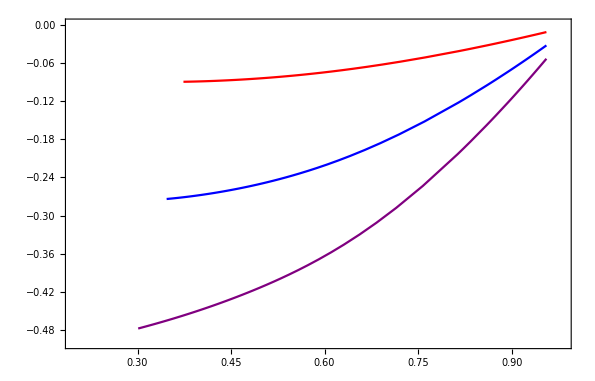

/Users/jaimeredondoyuste/Library/Mathematica/Applications/MathematicaQNM/Fig_Example.png

```mathematica
<<MaTeX`
fig = ParametricPlot[{{Re[ω1[a]],Im[ω1[a]]},{Re[ω2[a]],Im[ω2[a]]},{Re[ω3[a]],Im[ω3[a]]}},{a,0,0.999},PlotRange->{{0.2,0.98},{-0.5,0}},Frame->True,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},FrameLabel->{MaTeX["\\rm{Re} (\\omega_n)",Magnification->1.5],MaTeX["\\rm{Im} (\\omega_n)",Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["n=1",Magnification->1.2],MaTeX["n=2",Magnification->1.2],MaTeX["n=3",Magnification->1.2]},LegendFunction->"Panel"],{0.85,0.2}],PlotStyle->{Red,Blue,Purple},PlotLabel-> MaTeX["(\\ell, m) = (2, 2)", Magnification->1.8]]
Export["/Users/jaimeredondoyuste/Library/Mathematica/Applications/MathematicaQNM/Fig_Example.png", fig]
```